# Preparation

## Dataset

```mathematica
linearDS=Dataset[{<|"Nodes Count"->5,"Oracle Queries"->2,"Separator Ratio"->1.15575|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator Ratio"->1.09812|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator Ratio"->1.0482|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator Ratio"->2.24973|>,<|"Nodes Count"->5,"Oracle Queries"->2,"Separator Ratio"->0.916303|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator Ratio"->1.49075|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator Ratio"->1.99729|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator Ratio"->1.50533|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator Ratio"->1.03002|>,<|"Nodes Count"->10,"Oracle Queries"->3,"Separator Ratio"->1.14893|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator Ratio"->1.3837|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator Ratio"->2.36602|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator Ratio"->1.12487|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator Ratio"->1.28391|>,<|"Nodes Count"->15,"Oracle Queries"->4,"Separator Ratio"->3.02958|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator Ratio"->1.45622|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator Ratio"->1.35035|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator Ratio"->2.60995|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator Ratio"->3.07594|>,<|"Nodes Count"->25,"Oracle Queries"->5,"Separator Ratio"->1.56515|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator Ratio"->1.71779|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator Ratio"->1.64847|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator Ratio"->1.85987|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator Ratio"->2.23702|>,<|"Nodes Count"->50,"Oracle Queries"->7,"Separator Ratio"->1.31147|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator Ratio"->1.86845|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator Ratio"->1.58246|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator Ratio"->1.88399|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator Ratio"->1.64876|>,<|"Nodes Count"->100,"Oracle Queries"->10,"Separator Ratio"->1.27607|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator Ratio"->2.28718|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator Ratio"->2.53496|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator Ratio"->2.04462|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator Ratio"->1.2226|>,<|"Nodes Count"->150,"Oracle Queries"->13,"Separator Ratio"->1.65733|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator Ratio"->3.45445|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator Ratio"->1.76679|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator Ratio"->2.36316|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator Ratio"->1.45194|>,<|"Nodes Count"->250,"Oracle Queries"->16,"Separator Ratio"->1.44463|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator Ratio"->1.38221|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator Ratio"->1.43984|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator Ratio"->1.86843|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator Ratio"->1.34566|>,<|"Nodes Count"->500,"Oracle Queries"->23,"Separator Ratio"->1.43897|>,<|"Nodes Count"->5000,"Oracle Queries"->71,"Separator Ratio"->1.32919|>,<|"Nodes Count"->5000,"Oracle Queries"->71,"Separator Ratio"->1.15658|>,<|"Nodes Count"->5000,"Oracle Queries"->71,"Separator Ratio"->1.21663|>,<|"Nodes Count"->5000,"Oracle Queries"->71,"Separator Ratio"->1.20117|>,<|"Nodes Count"->5000,"Oracle Queries"->71,"Separator Ratio"->1.26417|>,<|"Nodes Count"->10000,"Oracle Queries"->100,"Separator Ratio"->1.12243|>,<|"Nodes Count"->10000,"Oracle Queries"->100,"Separator Ratio"->1.11275|>,<|"Nodes Count"->10000,"Oracle Queries"->100,"Separator Ratio"->1.13845|>,<|"Nodes Count"->10000,"Oracle Queries"->100,"Separator Ratio"->1.78681|>,<|"Nodes Count"->10000,"Oracle Queries"->100,"Separator Ratio"->1.25417|>}]
```

## Prelim Tests

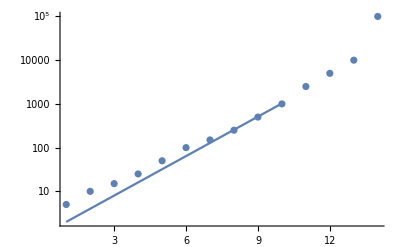

```mathematica
Show[LogPlot[2^x,{x,1,10}],ListLogPlot[{5,10,15,25,50,100,150,250,500,1000,2500,5000,10000,100000}],PlotRange->All]
```

# Usage

## Cleaning

```mathematica
meansDS=linearDS[GroupBy["Nodes Count"],Mean]
```

```mathematica
stdDS=linearDS[GroupBy["Nodes Count"],StandardDeviation]
```

```mathematica
sepValues=Values[List@@meansDS[[All,{"Nodes Count","Separator Ratio"}]]]//Normal;
```

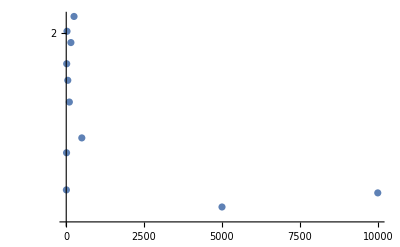

```mathematica
lplot=ListLogPlot[sepValues]
```

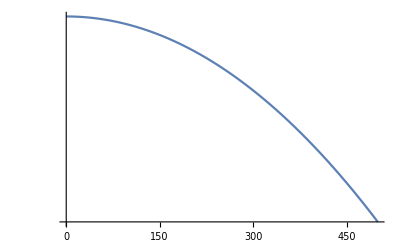

```mathematica
With[{expr=(a x^2+b)/.With[{first=First[sepValues],last=Last[sepValues]},With[{x1=First[first],y1=Last[first],xn=First[last],yn=Last[last]},Solve[{a x1^2+b==y1,a xn^2+b==yn},{a,b}]]][[1]]},refplot=LogPlot[Evaluate[expr],{x,0,500}]]
```

```mathematica
Show[lplot]
```

-Graphics-

```mathematica
List@@linearDS[[4,{"Nodes Count","Separator Ratio"}]]//Normal
```

{5,2.24973}

```mathematica
Length[linearDS]/Length[meansDS]
```

5

```mathematica
pointsOf[column_]:=Table[Point[List@@linearDS[[i,{"Nodes Count",column}]]//Normal],{i,1,Length[linearDS]}];
```

```mathematica
pointsOf["Separator Ratio"]
```

{Point[{5,1.15575}],Point[{5,1.09812}],Point[{5,1.0482}],Point[{5,2.24973}],Point[{5,0.916303}],Point[{10,1.49075}],Point[{10,1.99729}],Point[{10,1.50533}],Point[{10,1.03002}],Point[{10,1.14893}],Point[{15,1.3837}],Point[{15,2.36602}],Point[{15,1.12487}],Point[{15,1.28391}],Point[{15,3.02958}],Point[{25,1.45622}],Point[{25,1.35035}],Point[{25,2.60995}],Point[{25,3.07594}],Point[{25,1.56515}],Point[{50,1.71779}],Point[{50,1.64847}],Point[{50,1.85987}],Point[{50,2.23702}],Point[{50,1.31147}],Point[{100,1.86845}],Point[{100,1.58246}],Point[{100,1.88399}],Point[{100,1.64876}],Point[{100,1.27607}],Point[{150,2.28718}],Point[{150,2.53496}],Point[{150,2.04462}],Point[{150,1.2226}],Point[{150,1.65733}],Point[{250,3.45445}],Point[{250,1.76679}],Point[{250,2.36316}],Point[{250,1.45194}],Point[{250,1.44463}],Point[{500,1.38221}],Point[{500,1.43984}],Point[{500,1.86843}],Point[{500,1.34566}],Point[{500,1.43897}],Point[{5000,1.32919}],Point[{5000,1.15658}],Point[{5000,1.21663}],Point[{5000,1.20117}],Point[{5000,1.26417}],Point[{10000,1.12243}],Point[{10000,1.11275}],Point[{10000,1.13845}],Point[{10000,1.78681}],Point[{10000,1.25417}]}

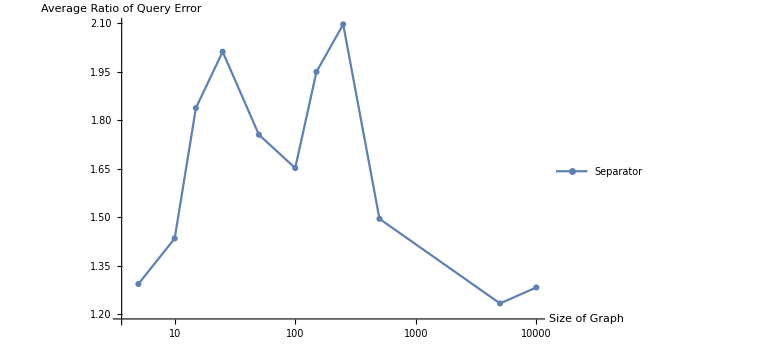

```mathematica
ListLogLinearPlot[sepValues,PlotRange->All,PlotLegends->{"Separator"},AxesLabel->{"Size of Graph","Average Ratio of Query Error"},Joined->True,PlotMarkers->Automatic,ImageSize->Large,Epilog->{Blue,PointSize[Small],pointsOf["Separator Ratio"]}]
```